```mathematica
ClearAll["Global`*"]
```

```mathematica
Series[(1/n+x)/(1/c+(c/n x)/c^2),{x,0,3}]
```

c/n+(c-c/n^2) x-(c (-1+n^2) x^2)/n^3+(c (-1+n^2) x^3)/n^4+O[x]^4

```mathematica
Series[(c/n+w)/(1+(c/n w)/c^2),{w,0,3}]
```

c/n+(1-1/n^2) w+((1-n^2) w^2)/(c n^3)+((-1+n^2) w^3)/(c^2 n^4)+O[w]^4

```mathematica
Plot[Cos[9*2π x]+Cos[10*2π x],{x,0,5}]
```

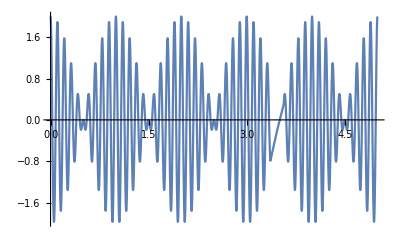

```mathematica
Cos[a x]+Cos[b x]//TrigFactor
```

2 Cos[(a x)/2-(b x)/2] Cos[(a x)/2+(b x)/2]